## |J|^2 at large k, first term

```mathematica
ClearAll[temp1];
temp1=(1+cb31)/b31^2+(1+cb41)/b41^2+(1+cb32)/b32^2+(1+cb42)/b42^2+(x34^2-b31^2-b41^2)/(2 b31^2 b41^2)(1+cb31+cb41+c34)+(x12^2-b31^2-b32^2)/(2 b31^2 b32^2)(1+cb31+cb32+c12)-(x1432^2-b31^2-b42^2)/(2 b31^2 b42^2)(c12+cb32+cb41+c34)-(x1342^2-b41^2-b32^2)/(2 b32^2 b41^2)(c12+cb42+cb31+c34)+(x12^2-b41^2-b42^2)/(2 b41^2 b42^2)(1+cb41+cb42+c12)+(x34^2-b32^2-b42^2)/(2 b32^2 b42^2)(1+cb32+cb42+c34);
```

```mathematica
Cx1432=Coefficient[temp1,x1432^2]//Simplify
Cx1342=Coefficient[temp1,x1342^2]//Simplify
```

-(c12+c34+cb32+cb41)/(2 b31^2 b42^2)

-(c12+c34+cb31+cb42)/(2 b32^2 b41^2)

```mathematica
Cx12=Coefficient[temp1/.{x1432:>0,x1342:>0},x12^2]//Simplify
Cx34=Coefficient[temp1/.{x1432:>0,x1342:>0},x34^2]//Simplify
```

1/2 ((c12+cb31+cb32+1)/(b31^2 b32^2)+(c12+cb41+cb42+1)/(b41^2 b42^2))

1/2 ((c34+cb31+cb41+1)/(b31^2 b41^2)+(c34+cb32+cb42+1)/(b32^2 b42^2))

```mathematica
temp1-(Cx1432*x1432^2+Cx1342*x1342^2+Cx12*x12^2+Cx34*x34^2)//Simplify
```

```mathematica
ClearAll[temp2];
temp2=(Cx1432*x1432^2+Cx1342*x1342^2+Cx12*x12^2+Cx34*x34^2);
```

```mathematica
temp2//Variables
```

{b31,b32,c12,cb31,cb32,b41,b42,cb41,cb42,x12,c34,x1342,x1432,x34}

```mathematica
ClearAll[NSP];
NSP[x_,y1_+y2_]:=NSP[x,y1]+NSP[x,y2];
NSP[x1_+x2_,y_]:=NSP[x1,y]+NSP[x2,y];
NSP[x_,b]/;x=!=b&&x=!=k:=NSP[b,x];
NSP[x_]:=NSP[x,x];
NSP[-x_,y_]:=-NSP[x,y];
NSP[x_,-y_]:=-NSP[x,y];
NSP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=NSP[x1,x];
NSP[x_,x2]/;!FreeQ[{x3,x4},x]:=NSP[x2,x];
NSP[x4,x3]:=NSP[x3,x4];
```

```mathematica
ClearAll[temp3];
temp3=2*temp2/.{b31:>√NSP[b-x3+x1],b32:>√NSP[b-x3+x2],b41:>√NSP[b-x4+x1],b42:>√NSP[b-x4+x2],x12:>√NSP[x1-x2],x1342:>√NSP[x1+x3-x4-x2],x1432:>√NSP[x1+x4-x3-x2],x34:>√NSP[x3-x4]}/.{c12:>Cos[NSP[k,x1-x2]],cb31:>Cos[NSP[k,b-x3+x1]],cb32:>Cos[NSP[k,b-x3+x2]],cb41:>Cos[NSP[k,b-x4+x1]],cb42:>Cos[NSP[k,b-x4+x2]],c34:>Cos[NSP[k,x3-x4]]}
```

2 (-(((-2 NSP(x1,x2)-2 NSP(x1,x3)+2 NSP(x1,x4)+NSP(x1,x1)+2 NSP(x2,x3)-2 NSP(x2,x4)+NSP(x2,x2)-2 NSP(x3,x4)+NSP(x3,x3)+NSP(x4,x4)) (cos(NSP(k,b)+NSP(k,x1)-NSP(k,x4))+cos(NSP(k,b)+NSP(k,x2)-NSP(k,x3))+cos(NSP(k,x1)-NSP(k,x2))+cos(NSP(k,x3)-NSP(k,x4))))/(2 (2 NSP(b,x1)-2 NSP(b,x3)+NSP(b,b)-2 NSP(x1,x3)+NSP(x1,x1)+NSP(x3,x3)) (2 NSP(b,x2)-2 NSP(b,x4)+NSP(b,b)-2 NSP(x2,x4)+NSP(x2,x2)+NSP(x4,x4))))-((-2 NSP(x1,x2)+2 NSP(x1,x3)-2 NSP(x1,x4)+NSP(x1,x1)-2 NSP(x2,x3)+2 NSP(x2,x4)+NSP(x2,x2)-2 NSP(x3,x4)+NSP(x3,x3)+NSP(x4,x4)) (cos(NSP(k,b)+NSP(k,x1)-NSP(k,x3))+cos(NSP(k,b)+NSP(k,x2)-NSP(k,x4))+cos(NSP(k,x1)-NSP(k,x2))+cos(NSP(k,x3)-NSP(k,x4))))/(2 (2 NSP(b,x1)-2 NSP(b,x4)+NSP(b,b)-2 NSP(x1,x4)+NSP(x1,x1)+NSP(x4,x4)) (2 NSP(b,x2)-2 NSP(b,x3)+NSP(b,b)-2 NSP(x2,x3)+NSP(x2,x2)+NSP(x3,x3)))+1/2 (-2 NSP(x3,x4)+NSP(x3,x3)+NSP(x4,x4)) ((cos(NSP(k,b)+NSP(k,x1)-NSP(k,x3))+cos(NSP(k,b)+NSP(k,x1)-NSP(k,x4))+cos(NSP(k,x3)-NSP(k,x4))+1)/((2 NSP(b,x1)-2 NSP(b,x3)+NSP(b,b)-2 NSP(x1,x3)+NSP(x1,x1)+NSP(x3,x3)) (2 NSP(b,x1)-2 NSP(b,x4)+NSP(b,b)-2 NSP(x1,x4)+NSP(x1,x1)+NSP(x4,x4)))+(cos(NSP(k,b)+NSP(k,x2)-NSP(k,x3))+cos(NSP(k,b)+NSP(k,x2)-NSP(k,x4))+cos(NSP(k,x3)-NSP(k,x4))+1)/((2 NSP(b,x2)-2 NSP(b,x3)+NSP(b,b)-2 NSP(x2,x3)+NSP(x2,x2)+NSP(x3,x3)) (2 NSP(b,x2)-2 NSP(b,x4)+NSP(b,b)-2 NSP(x2,x4)+NSP(x2,x2)+NSP(x4,x4))))+1/2 (-2 NSP(x1,x2)+NSP(x1,x1)+NSP(x2,x2)) ((cos(NSP(k,b)+NSP(k,x1)-NSP(k,x3))+cos(NSP(k,b)+NSP(k,x2)-NSP(k,x3))+cos(NSP(k,x1)-NSP(k,x2))+1)/((2 NSP(b,x1)-2 NSP(b,x3)+NSP(b,b)-2 NSP(x1,x3)+NSP(x1,x1)+NSP(x3,x3)) (2 NSP(b,x2)-2 NSP(b,x3)+NSP(b,b)-2 NSP(x2,x3)+NSP(x2,x2)+NSP(x3,x3)))+(cos(NSP(k,b)+NSP(k,x1)-NSP(k,x4))+cos(NSP(k,b)+NSP(k,x2)-NSP(k,x4))+cos(NSP(k,x1)-NSP(k,x2))+1)/((2 NSP(b,x1)-2 NSP(b,x4)+NSP(b,b)-2 NSP(x1,x4)+NSP(x1,x1)+NSP(x4,x4)) (2 NSP(b,x2)-2 NSP(b,x4)+NSP(b,b)-2 NSP(x2,x4)+NSP(x2,x2)+NSP(x4,x4)))))

```mathematica
ClearAll[var];
var=(temp3/.Cos[x_]:>x//Variables)//Sort
%//Length
```

{NSP(b,b),NSP(b,x1),NSP(b,x2),NSP(b,x3),NSP(b,x4),NSP(k,b),NSP(k,x1),NSP(k,x2),NSP(k,x3),NSP(k,x4),NSP(x1,x1),NSP(x1,x2),NSP(x1,x3),NSP(x1,x4),NSP(x2,x2),NSP(x2,x3),NSP(x2,x4),NSP(x3,x3),NSP(x3,x4),NSP(x4,x4)}

20

```mathematica
ClearAll[rplc];
rplc=Thread[Rule[var,{NSP1[1],NSP1[2],NSP1[3],NSP1[4],NSP1[5],NSP1[6],NSP1[8],NSP1[9],NSP1[10],NSP1[11],NSP1[12],NSP1[13],NSP1[14],NSP1[15],NSP1[16],NSP1[17],NSP1[18],NSP1[19],NSP1[20],NSP1[21]}]]
```

{NSP(b,b)→NSP1(1),NSP(b,x1)→NSP1(2),NSP(b,x2)→NSP1(3),NSP(b,x3)→NSP1(4),NSP(b,x4)→NSP1(5),NSP(k,b)→NSP1(6),NSP(k,x1)→NSP1(8),NSP(k,x2)→NSP1(9),NSP(k,x3)→NSP1(10),NSP(k,x4)→NSP1(11),NSP(x1,x1)→NSP1(12),NSP(x1,x2)→NSP1(13),NSP(x1,x3)→NSP1(14),NSP(x1,x4)→NSP1(15),NSP(x2,x2)→NSP1(16),NSP(x2,x3)→NSP1(17),NSP(x2,x4)→NSP1(18),NSP(x3,x3)→NSP1(19),NSP(x3,x4)→NSP1(20),NSP(x4,x4)→NSP1(21)}

```mathematica
ClearAll[temp4];
temp4=temp3/.rplc//InputForm
```

2*(-((Cos[NSP1[8] - NSP1[9]] + Cos[NSP1[6] + NSP1[9] - NSP1[10]] + Cos[NSP1[6] + NSP1[8] - NSP1[11]] + Cos[NSP1[10] - NSP1[11]])*
     (NSP1[12] - 2*NSP1[13] - 2*NSP1[14] + 2*NSP1[15] + NSP1[16] + 2*NSP1[17] - 2*NSP1[18] + NSP1[19] - 2*NSP1[20] + NSP1[21]))/
   (2*(NSP1[1] + 2*NSP1[2] - 2*NSP1[4] + NSP1[12] - 2*NSP1[14] + NSP1[19])*(NSP1[1] + 2*NSP1[3] - 2*NSP1[5] + NSP1[16] - 2*NSP1[18] + NSP1[21])) - 
  ((Cos[NSP1[8] - NSP1[9]] + Cos[NSP1[6] + NSP1[8] - NSP1[10]] + Cos[NSP1[6] + NSP1[9] - NSP1[11]] + Cos[NSP1[10] - NSP1[11]])*
    (NSP1[12] - 2*NSP1[13] + 2*NSP1[14] - 2*NSP1[15] + NSP1[16] - 2*NSP1[17] + 2*NSP1[18] + NSP1[19] - 2*NSP1[20] + NSP1[21]))/
   (2*(NSP1[1] + 2*NSP1[3] - 2*NSP1[4] + NSP1[16] - 2*NSP1[17] + NSP1[19])*(NSP1[1] + 2*NSP1[2] - 2*NSP1[5] + NSP1[12] - 2*NSP1[15] + NSP1[21])) + 
  ((NSP1[19] - 2*NSP1[20] + NSP1[21])*((1 + Cos[NSP1[6] + NSP1[8] - NSP1[10]] + Cos[NSP1[6] + NSP1[8] - NSP1[11]] + Cos[NSP1[10] - NSP1[11]])/
      ((NSP1[1] + 2*NSP1[2] - 2*NSP1[4] + NSP1[12] - 2*NSP1[14] + NSP1[19])*(NSP1[1] + 2*NSP1[2] - 2*NSP1[5] + NSP1[12] - 2*NSP1[15] + NSP1[21])) + 
     (1 + Cos[NSP1[6] + NSP1[9] - NSP1[10]] + Cos[NSP1[6] + NSP1[9] - NSP1[11]] + Cos[NSP1[10] - NSP1[11]])/
      ((NSP1[1] + 2*NSP1[3] - 2*NSP1[4] + NSP1[16] - 2*NSP1[17] + NSP1[19])*(NSP1[1] + 2*NSP1[3] - 2*NSP1[5] + NSP1[16] - 2*NSP1[18] + NSP1[21]))))/2 + 
  ((NSP1[12] - 2*NSP1[13] + NSP1[16])*((1 + Cos[NSP1[8] - NSP1[9]] + Cos[NSP1[6] + NSP1[8] - NSP1[10]] + Cos[NSP1[6] + NSP1[9] - NSP1[10]])/
      ((NSP1[1] + 2*NSP1[2] - 2*NSP1[4] + NSP1[12] - 2*NSP1[14] + NSP1[19])*(NSP1[1] + 2*NSP1[3] - 2*NSP1[4] + NSP1[16] - 2*NSP1[17] + NSP1[19])) + 
     (1 + Cos[NSP1[8] - NSP1[9]] + Cos[NSP1[6] + NSP1[8] - NSP1[11]] + Cos[NSP1[6] + NSP1[9] - NSP1[11]])/
      ((NSP1[1] + 2*NSP1[2] - 2*NSP1[5] + NSP1[12] - 2*NSP1[15] + NSP1[21])*(NSP1[1] + 2*NSP1[3] - 2*NSP1[5] + NSP1[16] - 2*NSP1[18] + NSP1[21]))))/2)

```mathematica
temp3/.rplc//Variables
```

{cos(NSP1(8)-NSP1(9)),cos(NSP1(6)+NSP1(8)-NSP1(10)),cos(NSP1(6)+NSP1(9)-NSP1(10)),cos(NSP1(6)+NSP1(8)-NSP1(11)),cos(NSP1(6)+NSP1(9)-NSP1(11)),cos(NSP1(10)-NSP1(11)),NSP1(1),NSP1(2),NSP1(3),NSP1(4),NSP1(5),NSP1(12),NSP1(13),NSP1(14),NSP1(15),NSP1(16),NSP1(17),NSP1(18),NSP1(19),NSP1(20),NSP1(21)}

```mathematica
Integrate[Cos[kx Cos[θk-θx]],{θk,0,2π},Assumptions->kx∈Reals]
```

2 π 0Abs[kx]

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

-2 π cos(2 θx) 2Abs[kx]

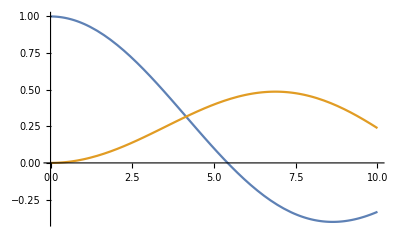

```mathematica
Plot[{BesselJ[0,0.444x],BesselJ[2,0.444x]},{x,0,10}]
```

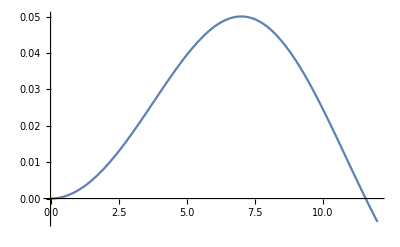

```mathematica
Plot[BesselJ[2,0.444x]/(10+BesselJ[0,0.444x]),{x,0,12}]
```

## |J|^2 at large k

### Check manual calculation

```mathematica
ClearAll[Ai];
Ai[x_]:=ⅈ/(2π)(1+Exp[ⅈ SP[k,x]])/(SP[k]^2 SP[x])(SP[k]FV[x,i]-2SP[k,x]FV[k,i])+ⅈ/π(SP[k,x]FV[k,i])/(SP[k]^2 SP[x])Exp[ⅈ SP[k,x]];
```

```mathematica
ClearAll[Ji];
Ji=Ai[-x3+x1]Exp[-ⅈ SP[k,x1]]-Ai[-x4+x1]Exp[-ⅈ SP[k,x1]]-Ai[-x3+x2]Exp[-ⅈ SP[k,x2]]+Ai[-x4+x2]Exp[-ⅈ SP[k,x2]]
```

ⅇ^(-ⅈ SP(k,x1)) ((ⅈ (1+ⅇ^(ⅈ (SP(k,x1)-SP(k,x3)))) (SP(k) FV(x1-x3,i)-2 FV(k,i) (SP(k,x1)-SP(k,x3))))/(2 π (SP(k))^2 SP(x1-x3))+(ⅈ FV(k,i) ⅇ^(ⅈ (SP(k,x1)-SP(k,x3))) (SP(k,x1)-SP(k,x3)))/(π (SP(k))^2 SP(x1-x3)))-ⅇ^(-ⅈ SP(k,x1)) ((ⅈ (1+ⅇ^(ⅈ (SP(k,x1)-SP(k,x4)))) (SP(k) FV(x1-x4,i)-2 FV(k,i) (SP(k,x1)-SP(k,x4))))/(2 π (SP(k))^2 SP(x1-x4))+(ⅈ FV(k,i) ⅇ^(ⅈ (SP(k,x1)-SP(k,x4))) (SP(k,x1)-SP(k,x4)))/(π (SP(k))^2 SP(x1-x4)))-ⅇ^(-ⅈ SP(k,x2)) ((ⅈ (1+ⅇ^(ⅈ (SP(k,x2)-SP(k,x3)))) (SP(k) FV(x2-x3,i)-2 FV(k,i) (SP(k,x2)-SP(k,x3))))/(2 π (SP(k))^2 SP(x2-x3))+(ⅈ FV(k,i) ⅇ^(ⅈ (SP(k,x2)-SP(k,x3))) (SP(k,x2)-SP(k,x3)))/(π (SP(k))^2 SP(x2-x3)))+ⅇ^(-ⅈ SP(k,x2)) ((ⅈ (1+ⅇ^(ⅈ (SP(k,x2)-SP(k,x4)))) (SP(k) FV(x2-x4,i)-2 FV(k,i) (SP(k,x2)-SP(k,x4))))/(2 π (SP(k))^2 SP(x2-x4))+(ⅈ FV(k,i) ⅇ^(ⅈ (SP(k,x2)-SP(k,x4))) (SP(k,x2)-SP(k,x4)))/(π (SP(k))^2 SP(x2-x4)))

```mathematica
ClearAll[JiCC];
JiCC=Ji/.Complex[x_,y_]:>Complex[x,-y]
```

ⅇ^(ⅈ SP(k,x1)) (-(ⅈ (1+ⅇ^(-ⅈ (SP(k,x1)-SP(k,x3)))) (SP(k) FV(x1-x3,i)-2 FV(k,i) (SP(k,x1)-SP(k,x3))))/(2 π (SP(k))^2 SP(x1-x3))-(ⅈ FV(k,i) ⅇ^(-ⅈ (SP(k,x1)-SP(k,x3))) (SP(k,x1)-SP(k,x3)))/(π (SP(k))^2 SP(x1-x3)))-ⅇ^(ⅈ SP(k,x1)) (-(ⅈ (1+ⅇ^(-ⅈ (SP(k,x1)-SP(k,x4)))) (SP(k) FV(x1-x4,i)-2 FV(k,i) (SP(k,x1)-SP(k,x4))))/(2 π (SP(k))^2 SP(x1-x4))-(ⅈ FV(k,i) ⅇ^(-ⅈ (SP(k,x1)-SP(k,x4))) (SP(k,x1)-SP(k,x4)))/(π (SP(k))^2 SP(x1-x4)))-ⅇ^(ⅈ SP(k,x2)) (-(ⅈ (1+ⅇ^(-ⅈ (SP(k,x2)-SP(k,x3)))) (SP(k) FV(x2-x3,i)-2 FV(k,i) (SP(k,x2)-SP(k,x3))))/(2 π (SP(k))^2 SP(x2-x3))-(ⅈ FV(k,i) ⅇ^(-ⅈ (SP(k,x2)-SP(k,x3))) (SP(k,x2)-SP(k,x3)))/(π (SP(k))^2 SP(x2-x3)))+ⅇ^(ⅈ SP(k,x2)) (-(ⅈ (1+ⅇ^(-ⅈ (SP(k,x2)-SP(k,x4)))) (SP(k) FV(x2-x4,i)-2 FV(k,i) (SP(k,x2)-SP(k,x4))))/(2 π (SP(k))^2 SP(x2-x4))-(ⅈ FV(k,i) ⅇ^(-ⅈ (SP(k,x2)-SP(k,x4))) (SP(k,x2)-SP(k,x4)))/(π (SP(k))^2 SP(x2-x4)))

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[J2s1];
J2s1=Ji*JiCC//Expand//ReplaceAll[#,{FV[x_,i]FV[y_,i]:>SP[x,y],FV[x_,i]^2:>SP[x,x]}]&(*//Simplify*)
```

-(2 (SP(k,x1))^2)/(π^2 (SP(k,k))^3 (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+(SP(k,x1))^2/(π^2 (SP(k,k))^3 (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3))^2)+326+(ⅇ^(-ⅈ (SP(k,x2)-SP(k,x4))) (SP(k,x2)-SP(k,x4)) SP(k,x4))/(2 π^2 (SP(k,k))^3 (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))^2)+(ⅇ^(ⅈ (SP(k,x2)-SP(k,x4))) (SP(k,x2)-SP(k,x4)) SP(k,x4))/(2 π^2 (SP(k,k))^3 (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))^2)+((SP(k,x2)-SP(k,x4)) SP(k,x4))/(π^2 (SP(k,k))^3 (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))^2)
 |  |  |  |

```mathematica
ClearAll[MyresT1];
MyresT1=2/(2π)^2 1/SP[k]^2((1+cb31)/b31^2+(1+cb41)/b41^2+(1+cb32)/b32^2+(1+cb42)/b42^2+(x34^2-b31^2-b41^2)/(2 b31^2 b41^2)(1+cb31+cb41+c34)+(x12^2-b31^2-b32^2)/(2 b31^2 b32^2)(1+cb31+cb32+c12)-(x1432^2-b31^2-b42^2)/(2 b31^2 b42^2)(c12+cb32+cb41+c34)-(x1342^2-b41^2-b32^2)/(2 b32^2 b41^2)(c12+cb42+cb31+c34)+(x12^2-b41^2-b42^2)/(2 b41^2 b42^2)(1+cb41+cb42+c12)+(x34^2-b32^2-b42^2)/(2 b32^2 b42^2)(1+cb32+cb42+c34));
```

```mathematica
Cx1432=Coefficient[MyresT1,x1432^2]//Simplify
Cx1342=Coefficient[MyresT1,x1342^2]//Simplify
```

-(c12+c34+cb32+cb41)/(4 π^2 b31^2 b42^2 (SP(k,k))^2)

-(c12+c34+cb31+cb42)/(4 π^2 b32^2 b41^2 (SP(k,k))^2)

```mathematica
Cx12=Coefficient[MyresT1/.{x1432:>0,x1342:>0},x12^2]//Simplify
Cx34=Coefficient[MyresT1/.{x1432:>0,x1342:>0},x34^2]//Simplify
```

(b31^2 b32^2 (c12+cb41+cb42+1)+b41^2 b42^2 (c12+cb31+cb32+1))/(4 π^2 b31^2 b32^2 b41^2 b42^2 (SP(k,k))^2)

(b31^2 b41^2 (c34+cb32+cb42+1)+b32^2 b42^2 (c34+cb31+cb41+1))/(4 π^2 b31^2 b32^2 b41^2 b42^2 (SP(k,k))^2)

```mathematica
MyresT1-(Cx1432*x1432^2+Cx1342*x1342^2+Cx12*x12^2+Cx34*x34^2)//Simplify
```

0

```mathematica
ClearAll[MyresT2];
MyresT2=-1/π^2 1/SP[k]^3((SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c31-(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c32-(SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c41+(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c42)
```

-(c31 ((SP(k,x31))/(SP(x31,x31))-(SP(k,x32))/(SP(x32,x32))) ((SP(k,x31))/(SP(x31,x31))-(SP(k,x41))/(SP(x41,x41)))-c32 ((SP(k,x31))/(SP(x31,x31))-(SP(k,x32))/(SP(x32,x32))) ((SP(k,x32))/(SP(x32,x32))-(SP(k,x42))/(SP(x42,x42)))-c41 ((SP(k,x31))/(SP(x31,x31))-(SP(k,x41))/(SP(x41,x41))) ((SP(k,x41))/(SP(x41,x41))-(SP(k,x42))/(SP(x42,x42)))+c42 ((SP(k,x32))/(SP(x32,x32))-(SP(k,x42))/(SP(x42,x42))) ((SP(k,x41))/(SP(x41,x41))-(SP(k,x42))/(SP(x42,x42))))/(π^2 (SP(k,k))^3)

```mathematica
ClearAll[Myres];
Myres=MyresT1+MyresT2/.{cb31:>c31,cb41:>c41,cb32:>c32,cb42:>c42,b31:>√SP[x31],b32:>√SP[x32],b41:>√SP[x41],b42:>√SP[x42],x1432:>√SP[x1432],x1342:>√SP[x1342],x12:>√SP[x12],x34:>√SP[x34]}/.{x31:>-x3+x1,x32:>-x3+x2,x12:>x1-x2,x41:>-x4+x1,x42:>-x4+x2,x1342:>x1+x3-x4-x2,x1432:>x1+x4-x3-x2,x34:>x3-x4}/.{c31:>Cos[SP[k,x1-x3]],c32:>Cos[SP[k,x2-x3]],c12:>Cos[SP[k,x1-x2]],c41:>Cos[SP[k,x1-x4]],c42:>Cos[SP[k,x2-x4]],c34:>Cos[SP[k,x3-x4]]}//TrigToExp;
```

```mathematica
Variables[Myres]
```

{SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4),SP(x1,x1),SP(x1,x2),SP(x1,x3),SP(x1,x4),SP(x2,x2),SP(x2,x3),SP(x2,x4),SP(x3,x3),SP(x3,x4),SP(x4,x4)}

```mathematica
J2s1//Variables
```

{SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4),SP(x1,x1),SP(x1,x2),SP(x1,x3),SP(x1,x4),SP(x2,x2),SP(x2,x3),SP(x2,x4),SP(x3,x3),SP(x3,x4),SP(x4,x4)}

```mathematica
J2s1-Myres//Simplify
```

0

```mathematica
MyresT1+MyresT2//Variables
```

{b31,cb31,b32,cb32,b41,cb41,b42,cb42,c12,x12,c34,x1342,x1432,x34,SP(k,k),c31,SP(k,x31),SP(x31,x31),SP(k,x32),SP(x32,x32),SP(k,x41),SP(x41,x41),c32,SP(k,x42),SP(x42,x42),c41,c42}

```mathematica
MyresT1+MyresT2/.{SP[x31,x31]:>ϵ^2 SP[x31,x31],SP[k,x31]:>ϵ SP[k,x31]};
Series[%,{ϵ,0,0}](*//Simplify*)
```

-(c31 (SP(k,x31))^2)/(π^2 ϵ^2 (SP(k,k))^3 (SP(x31,x31))^2)+(SP(k,x31) (c31 SP(x41,x41) SP(x42,x42) SP(k,x32)+c31 SP(x32,x32) SP(x42,x42) SP(k,x41)-c32 SP(x32,x32) SP(x41,x41) SP(k,x42)+c32 SP(x41,x41) SP(x42,x42) SP(k,x32)-c41 SP(x32,x32) SP(x41,x41) SP(k,x42)+c41 SP(x32,x32) SP(x42,x42) SP(k,x41)))/(π^2 ϵ (SP(k,k))^3 SP(x31,x31) SP(x32,x32) SP(x41,x41) SP(x42,x42))+((((-b31^2-b32^2+x12^2) (c12+cb31+cb32+1))/(2 b31^2 b32^2)+((-b31^2-b41^2+x34^2) (c34+cb31+cb41+1))/(2 b31^2 b41^2)-((-b31^2-b42^2+x1432^2) (c12+c34+cb32+cb41))/(2 b31^2 b42^2)+(cb31+1)/b31^2-((-b32^2-b41^2+x1342^2) (c12+c34+cb31+cb42))/(2 b32^2 b41^2)+((-b32^2-b42^2+x34^2) (c34+cb32+cb42+1))/(2 b32^2 b42^2)+(cb32+1)/b32^2+((-b41^2-b42^2+x12^2) (c12+cb41+cb42+1))/(2 b41^2 b42^2)+(cb41+1)/b41^2+(cb42+1)/b42^2)/(2 π^2 (SP(k,k))^2)+(-(c31 SP(k,x32) SP(k,x41))/(SP(x32,x32) SP(x41,x41))-(c32 SP(k,x32) ((SP(k,x32))/(SP(x32,x32))-(SP(k,x42))/(SP(x42,x42))))/(SP(x32,x32))-(c41 SP(k,x41) ((SP(k,x41))/(SP(x41,x41))-(SP(k,x42))/(SP(x42,x42))))/(SP(x41,x41))-c42 ((SP(k,x32))/(SP(x32,x32))-(SP(k,x42))/(SP(x42,x42))) ((SP(k,x41))/(SP(x41,x41))-(SP(k,x42))/(SP(x42,x42))))/(π^2 (SP(k,k))^3))+O(ϵ^1)

### Create Numerical Code Input

```mathematica
ClearAll[var1];
var1=Myres//Variables//Sort
```

{SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4),SP(x1,x1),SP(x1,x2),SP(x1,x3),SP(x1,x4),SP(x2,x2),SP(x2,x3),SP(x2,x4),SP(x3,x3),SP(x3,x4),SP(x4,x4)}

```mathematica
ClearAll[var2];
var2=Table[NSP[ii+6],{ii,1,Length[var1]}]
```

{NSP(7),NSP(8),NSP(9),NSP(10),NSP(11),NSP(12),NSP(13),NSP(14),NSP(15),NSP(16),NSP(17),NSP(18),NSP(19),NSP(20),NSP(21)}

```mathematica
ClearAll[rplc];
rplc=Thread[var1->var2]
```

{SP(k,k)→NSP(7),SP(k,x1)→NSP(8),SP(k,x2)→NSP(9),SP(k,x3)→NSP(10),SP(k,x4)→NSP(11),SP(x1,x1)→NSP(12),SP(x1,x2)→NSP(13),SP(x1,x3)→NSP(14),SP(x1,x4)→NSP(15),SP(x2,x2)→NSP(16),SP(x2,x3)→NSP(17),SP(x2,x4)→NSP(18),SP(x3,x3)→NSP(19),SP(x3,x4)→NSP(20),SP(x4,x4)→NSP(21)}

```mathematica
ClearAll[input];
input=Myres/.rplc;
%//Variables
```

{NSP(7),NSP(8),NSP(9),NSP(10),NSP(11),NSP(12),NSP(13),NSP(14),NSP(15),NSP(16),NSP(17),NSP(18),NSP(19),NSP(20),NSP(21)}

```mathematica
input//InputForm
```

((1 + (E^(I*NSP[8] - I*NSP[10]) + E^((-I)*NSP[8] + I*NSP[10]))/2)/(NSP[12] - 2*NSP[14] + NSP[19]) + 
   (1 + (E^(I*NSP[9] - I*NSP[10]) + E^((-I)*NSP[9] + I*NSP[10]))/2)/(NSP[16] - 2*NSP[17] + NSP[19]) + 
   ((1 + (E^(I*NSP[8] - I*NSP[9]) + E^((-I)*NSP[8] + I*NSP[9]))/2 + (E^(I*NSP[8] - I*NSP[10]) + E^((-I)*NSP[8] + I*NSP[10]))/2 + 
      (E^(I*NSP[9] - I*NSP[10]) + E^((-I)*NSP[9] + I*NSP[10]))/2)*(-2*NSP[13] + 2*NSP[14] + 2*NSP[17] - 2*NSP[19]))/
    (2*(NSP[12] - 2*NSP[14] + NSP[19])*(NSP[16] - 2*NSP[17] + NSP[19])) + (1 + (E^(I*NSP[8] - I*NSP[11]) + E^((-I)*NSP[8] + I*NSP[11]))/2)/
    (NSP[12] - 2*NSP[15] + NSP[21]) + ((1 + (E^(I*NSP[8] - I*NSP[10]) + E^((-I)*NSP[8] + I*NSP[10]))/2 + 
      (E^(I*NSP[8] - I*NSP[11]) + E^((-I)*NSP[8] + I*NSP[11]))/2 + (E^(I*NSP[10] - I*NSP[11]) + E^((-I)*NSP[10] + I*NSP[11]))/2)*
     (-2*NSP[12] + 2*NSP[14] + 2*NSP[15] - 2*NSP[20]))/(2*(NSP[12] - 2*NSP[14] + NSP[19])*(NSP[12] - 2*NSP[15] + NSP[21])) - 
   (((E^(I*NSP[8] - I*NSP[9]) + E^((-I)*NSP[8] + I*NSP[9]))/2 + (E^(I*NSP[8] - I*NSP[10]) + E^((-I)*NSP[8] + I*NSP[10]))/2 + 
      (E^(I*NSP[9] - I*NSP[11]) + E^((-I)*NSP[9] + I*NSP[11]))/2 + (E^(I*NSP[10] - I*NSP[11]) + E^((-I)*NSP[10] + I*NSP[11]))/2)*
     (-2*NSP[13] + 2*NSP[14] + 2*NSP[18] - 2*NSP[20]))/(2*(NSP[16] - 2*NSP[17] + NSP[19])*(NSP[12] - 2*NSP[15] + NSP[21])) + 
   (1 + (E^(I*NSP[9] - I*NSP[11]) + E^((-I)*NSP[9] + I*NSP[11]))/2)/(NSP[16] - 2*NSP[18] + NSP[21]) - 
   (((E^(I*NSP[8] - I*NSP[9]) + E^((-I)*NSP[8] + I*NSP[9]))/2 + (E^(I*NSP[9] - I*NSP[10]) + E^((-I)*NSP[9] + I*NSP[10]))/2 + 
      (E^(I*NSP[8] - I*NSP[11]) + E^((-I)*NSP[8] + I*NSP[11]))/2 + (E^(I*NSP[10] - I*NSP[11]) + E^((-I)*NSP[10] + I*NSP[11]))/2)*
     (-2*NSP[13] + 2*NSP[15] + 2*NSP[17] - 2*NSP[20]))/(2*(NSP[12] - 2*NSP[14] + NSP[19])*(NSP[16] - 2*NSP[18] + NSP[21])) + 
   ((1 + (E^(I*NSP[9] - I*NSP[10]) + E^((-I)*NSP[9] + I*NSP[10]))/2 + (E^(I*NSP[9] - I*NSP[11]) + E^((-I)*NSP[9] + I*NSP[11]))/2 + 
      (E^(I*NSP[10] - I*NSP[11]) + E^((-I)*NSP[10] + I*NSP[11]))/2)*(-2*NSP[16] + 2*NSP[17] + 2*NSP[18] - 2*NSP[20]))/
    (2*(NSP[16] - 2*NSP[17] + NSP[19])*(NSP[16] - 2*NSP[18] + NSP[21])) + 
   ((1 + (E^(I*NSP[8] - I*NSP[9]) + E^((-I)*NSP[8] + I*NSP[9]))/2 + (E^(I*NSP[8] - I*NSP[11]) + E^((-I)*NSP[8] + I*NSP[11]))/2 + 
      (E^(I*NSP[9] - I*NSP[11]) + E^((-I)*NSP[9] + I*NSP[11]))/2)*(-2*NSP[13] + 2*NSP[15] + 2*NSP[18] - 2*NSP[21]))/
    (2*(NSP[12] - 2*NSP[15] + NSP[21])*(NSP[16] - 2*NSP[18] + NSP[21])))/(2*Pi^2*NSP[7]^2) - 
 (((E^(I*NSP[8] - I*NSP[10]) + E^((-I)*NSP[8] + I*NSP[10]))*((NSP[8] - NSP[10])/(NSP[12] - 2*NSP[14] + NSP[19]) - 
      (NSP[9] - NSP[10])/(NSP[16] - 2*NSP[17] + NSP[19]))*((NSP[8] - NSP[10])/(NSP[12] - 2*NSP[14] + NSP[19]) - 
      (NSP[8] - NSP[11])/(NSP[12] - 2*NSP[15] + NSP[21])))/2 - ((E^(I*NSP[9] - I*NSP[10]) + E^((-I)*NSP[9] + I*NSP[10]))*
     ((NSP[8] - NSP[10])/(NSP[12] - 2*NSP[14] + NSP[19]) - (NSP[9] - NSP[10])/(NSP[16] - 2*NSP[17] + NSP[19]))*
     ((NSP[9] - NSP[10])/(NSP[16] - 2*NSP[17] + NSP[19]) - (NSP[9] - NSP[11])/(NSP[16] - 2*NSP[18] + NSP[21])))/2 - 
   ((E^(I*NSP[8] - I*NSP[11]) + E^((-I)*NSP[8] + I*NSP[11]))*((NSP[8] - NSP[10])/(NSP[12] - 2*NSP[14] + NSP[19]) - 
      (NSP[8] - NSP[11])/(NSP[12] - 2*NSP[15] + NSP[21]))*((NSP[8] - NSP[11])/(NSP[12] - 2*NSP[15] + NSP[21]) - 
      (NSP[9] - NSP[11])/(NSP[16] - 2*NSP[18] + NSP[21])))/2 + ((E^(I*NSP[9] - I*NSP[11]) + E^((-I)*NSP[9] + I*NSP[11]))*
     ((NSP[9] - NSP[10])/(NSP[16] - 2*NSP[17] + NSP[19]) - (NSP[9] - NSP[11])/(NSP[16] - 2*NSP[18] + NSP[21]))*
     ((NSP[8] - NSP[11])/(NSP[12] - 2*NSP[15] + NSP[21]) - (NSP[9] - NSP[11])/(NSP[16] - 2*NSP[18] + NSP[21])))/2)/(Pi^2*NSP[7]^3)

### Integration

```mathematica
Integrate[Cos[kx Cos[θk-θx]],{θk,0,2π},Assumptions->kx∈Reals]
```

2 π 0Abs[kx]

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[θk-θ1]Cos[θk-θ2],{θk,0,2π},Assumptions->kx∈Reals]
```

(2 π 1kx cos(θ1-θ2))/kx-2 π 2kx cos(θ1-θx) cos(θ2-θx)

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

-2 π cos(2 θx) 2Abs[kx]

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[θk-θ1]Cos[θk-θ2]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

1/kx^2 π (2 2kx (6 cos(θ1+θ2-4 θx)-kx^2 cos(2 θx) cos(θ1-θx) cos(θ2-θx))+kx 1kx (cos(θ1+θ2)-3 cos(θ1+θ2-4 θx)))

## |J|^2 at Small k

### Check manual calculation

```mathematica
ClearAll[I0,I1,I23];
I0=Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4 Abs[ρ])]+EulerGamma);
```

```mathematica
ClearAll[I0e2];
I0e2=Series[I0,{η,0,2}]//ReplaceAll[#,Abs[ρ]^2:>ρ^2]&//FullSimplify//Normal
```

(η^2 ρ^2 (-4 log(η)-4 ℽ+3+log(16)))/(16 π)+(ⅈ η ρ (2 log(η)+2 ℽ-1-log(4)))/(4 π)+(log(η/2)+ℽ)/(2 π)

```mathematica
ClearAll[I1e2];
I1e2=η/(4π)Integrate[α Series[Exp[ⅈ α ρ η]/(√(α(1-α)))(BesselK[1,η √(α(1-α))]-1/(η √(α(1-α)))),{η,0,1}],{α,0,1}]
```

(η^2 (2 log(η)+2 ℽ-3-log(4)))/(32 π)

```mathematica
ClearAll[I23e1];
I23e1=-ⅈ/(4π)Integrate[Series[Exp[ⅈ α ρ η] BesselK[0,η √(α(1-α))],{η,0,1}],{α,0,1}]
```

-((η ρ-2 ⅈ) (log(η/2)+ℽ-1))/(8 π)

```mathematica
I0e2+I1e2-2ρ η I23e1//Simplify
```

(log(η/2)+ℽ)/(2 π)+(ⅈ η ρ)/(4 π)-(η^2 (-2 log(η)+2 ρ^2-2 ℽ+3+log(4)))/(32 π)+O(η^3)

```mathematica
ClearAll[Ai0];
Ai0=-1/SP[k] FV[k,i](I0e2+I1e2)+1/SP[k](2FV[k,i]SP[k,x]-SP[k]FV[x,i])I23e1/.ρ:>SP[k,x]/η/.η:>√(SP[k]SP[x])//Simplify//ReplaceAll[#,Log[(√(SP[k]SP[x]))/2]:>1/2 Log[(SP[k]SP[x])/4]]&//Simplify
```

(2 SP(k) FV(x,i) (SP(k,x)-2 ⅈ) (log(1/4 SP(k) SP(x))+2 ℽ-2)+FV(k,i) (2 (SP(k,x))^2-8 ⅈ SP(k,x)-8 log(SP(k) SP(x))-SP(k) SP(x) (log(1/4 SP(k) SP(x))+2 ℽ-3)-16 ℽ+log(65536)))/(32 π SP(k))

```mathematica
Variables[Ai0]
```

{FV(k,i),FV(x,i),log(1/4 SP(k) SP(x)),log(SP(k) SP(x)),SP(k),SP(x),SP(k,x)}

```mathematica
ClearAll[Aie2];
Aie2[x1_]:=Evaluate[Ai0/.x:>x1]
```

```mathematica
ClearAll[Jie2];
Jie2=Aie2[-x3+x1]Exp[-ⅈ SP[k,x1]]-Aie2[-x4+x1]Exp[-ⅈ SP[k,x1]]-Aie2[-x3+x2]Exp[-ⅈ SP[k,x2]]+Aie2[-x4+x2]Exp[-ⅈ SP[k,x2]]
```

(ⅇ^(-ⅈ SP(k,x1)) (2 SP(k) FV(x1-x3,i) (SP(k,x1-x3)-2 ⅈ) (log(1/4 SP(k) SP(x1-x3))+2 ℽ-2)+FV(k,i) (2 (SP(k,x1-x3))^2-8 ⅈ SP(k,x1-x3)-8 log(SP(k) SP(x1-x3))-SP(k) SP(x1-x3) (log(1/4 SP(k) SP(x1-x3))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))-(ⅇ^(-ⅈ SP(k,x1)) (2 SP(k) FV(x1-x4,i) (SP(k,x1-x4)-2 ⅈ) (log(1/4 SP(k) SP(x1-x4))+2 ℽ-2)+FV(k,i) (2 (SP(k,x1-x4))^2-8 ⅈ SP(k,x1-x4)-8 log(SP(k) SP(x1-x4))-SP(k) SP(x1-x4) (log(1/4 SP(k) SP(x1-x4))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))-(ⅇ^(-ⅈ SP(k,x2)) (2 SP(k) FV(x2-x3,i) (SP(k,x2-x3)-2 ⅈ) (log(1/4 SP(k) SP(x2-x3))+2 ℽ-2)+FV(k,i) (2 (SP(k,x2-x3))^2-8 ⅈ SP(k,x2-x3)-8 log(SP(k) SP(x2-x3))-SP(k) SP(x2-x3) (log(1/4 SP(k) SP(x2-x3))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))+(ⅇ^(-ⅈ SP(k,x2)) (2 SP(k) FV(x2-x4,i) (SP(k,x2-x4)-2 ⅈ) (log(1/4 SP(k) SP(x2-x4))+2 ℽ-2)+FV(k,i) (2 (SP(k,x2-x4))^2-8 ⅈ SP(k,x2-x4)-8 log(SP(k) SP(x2-x4))-SP(k) SP(x2-x4) (log(1/4 SP(k) SP(x2-x4))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))

```mathematica
ClearAll[Jie2CC];
Jie2CC=Jie2/.Complex[x_,y_]:>Complex[x,-y]
```

(ⅇ^(ⅈ SP(k,x1)) (2 SP(k) FV(x1-x3,i) (SP(k,x1-x3)+2 ⅈ) (log(1/4 SP(k) SP(x1-x3))+2 ℽ-2)+FV(k,i) (2 (SP(k,x1-x3))^2+8 ⅈ SP(k,x1-x3)-8 log(SP(k) SP(x1-x3))-SP(k) SP(x1-x3) (log(1/4 SP(k) SP(x1-x3))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))-(ⅇ^(ⅈ SP(k,x1)) (2 SP(k) FV(x1-x4,i) (SP(k,x1-x4)+2 ⅈ) (log(1/4 SP(k) SP(x1-x4))+2 ℽ-2)+FV(k,i) (2 (SP(k,x1-x4))^2+8 ⅈ SP(k,x1-x4)-8 log(SP(k) SP(x1-x4))-SP(k) SP(x1-x4) (log(1/4 SP(k) SP(x1-x4))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))-(ⅇ^(ⅈ SP(k,x2)) (2 SP(k) FV(x2-x3,i) (SP(k,x2-x3)+2 ⅈ) (log(1/4 SP(k) SP(x2-x3))+2 ℽ-2)+FV(k,i) (2 (SP(k,x2-x3))^2+8 ⅈ SP(k,x2-x3)-8 log(SP(k) SP(x2-x3))-SP(k) SP(x2-x3) (log(1/4 SP(k) SP(x2-x3))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))+(ⅇ^(ⅈ SP(k,x2)) (2 SP(k) FV(x2-x4,i) (SP(k,x2-x4)+2 ⅈ) (log(1/4 SP(k) SP(x2-x4))+2 ℽ-2)+FV(k,i) (2 (SP(k,x2-x4))^2+8 ⅈ SP(k,x2-x4)-8 log(SP(k) SP(x2-x4))-SP(k) SP(x2-x4) (log(1/4 SP(k) SP(x2-x4))+2 ℽ-3)-16 ℽ+log(65536))))/(32 π SP(k))

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[J2s1];
J2s1=Jie2*Jie2CC//Expand//ReplaceAll[#,{FV[x_,i]FV[y_,i]:>SP[x,y],FV[x_,i]^2:>SP[x,x]}]&(*//Simplify*)
```

-(ⅇ^(ⅈ SP(k,x1)-ⅈ SP(k,x2)) (SP(k,x3))^4)/(256 π^2 SP(k,k))-(ⅇ^(ⅈ SP(k,x2)-ⅈ SP(k,x1)) (SP(k,x3))^4)/(256 π^2 SP(k,k))+(SP(k,x3))^4/(128 π^2 SP(k,k))+(ⅇ^(ⅈ 1-1) SP(k,x1) 1^3)/(128 π^2 SP(k,k))+5708+(ⅇ^1 1 1)/(16 π^2 SP(k,k))-(log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (1)))/(8 π^2 SP(k,k))-(ⅇ^(ⅈ SP(k,x1)-ⅈ SP(k,x2)) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))))/(16 π^2 SP(k,k))-(ⅇ^(ⅈ SP(k,x2)-ⅈ SP(k,x1)) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))))/(16 π^2 SP(k,k))
 |  |  |  |

```mathematica
J2s1//Variables
```

{log(1/4 SP(k,k) (-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))),log(SP(k,k) (-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))),log(1/4 SP(k,k) (-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))),log(SP(k,k) (-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))),log(1/4 SP(k,k) (-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))),log(SP(k,k) (-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))),log(1/4 SP(k,k) (-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))),log(SP(k,k) (-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))),SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4),SP(x1,x1),SP(x1,x2),SP(x1,x3),SP(x1,x4),SP(x2,x2),SP(x2,x3),SP(x2,x4),SP(x3,x3),SP(x3,x4),SP(x4,x4)}

```mathematica
ClearAll[J2s2];
J2s2=Series[J2s1/.k:>ϵ k,{ϵ,0,0}]
```

(2 log(ϵ^2 SP(k,k) (-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))) log(ϵ^2 SP(k,k) (-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4)))+12+log^2(ϵ^2 SP(k,k) (-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))))/(16 π^2 ϵ^2 SP(k,k))+(297+log(1/4 ϵ^2 SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) log(ϵ^2 SP(k,k) (1)) SP(k,k) SP(x4,x4))/(64 π^2 SP(k,k))+O(ϵ^1)
 |  |  |  |

```mathematica
J2s2[[3,1]]/.ϵ:>1//Simplify
%/.{Log[SP[k,k]*(SP[x1,x1]-2*SP[x1,x3]+SP[x3,x3])]:>logk2+logx132,Log[SP[k,k]*(SP[x2,x2]-2*SP[x2,x3]+SP[x3,x3])]:>logk2+logx232,Log[SP[k,k]*(SP[x1,x1]-2*SP[x1,x4]+SP[x4,x4])]:>logk2+logx142,Log[SP[k,k]*(SP[x2,x2]-2*SP[x2,x4]+SP[x4,x4])]:>logk2+logx242}
```

(log(SP(k,k) (-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3)))-log(SP(k,k) (-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4)))-log(SP(k,k) (-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3)))+log(SP(k,k) (-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))))^2/(16 π^2 SP(k,k))

(logx132-logx142-logx232+logx242)^2/(16 π^2 SP(k,k))

```mathematica
J2s2[[3,2]]//Simplify
```

0

```mathematica
ClearAll[J2s3];
J2s3=J2s2[[3,3]]/.ϵ:>1//Simplify
```

-1/(64 π^2 SP(k,k))(2 (SP(k,x3))^2 log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-2 SP(k,k) SP(x1,x1) log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+4 SP(k,k) SP(x1,x3) log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-2 SP(k,k) SP(x3,x3) log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) (SP(k,x3))^2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) (SP(k,x3))^2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) (SP(k,x3))^2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) (SP(k,x4))^2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) (SP(k,x4))^2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x1) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x1) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x1) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x2) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x2) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(256) SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(16) SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+4 ℽ SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-6 SP(k,k) SP(x1,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(16) SP(k,k) SP(x1,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 ℽ SP(k,k) SP(x1,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+6 SP(k,k) SP(x1,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x2) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x2) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(16) SP(k,k) SP(x2,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-4 ℽ SP(k,k) SP(x2,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+6 SP(k,k) SP(x2,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(16) SP(k,k) SP(x2,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+4 ℽ SP(k,k) SP(x2,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-6 SP(k,k) SP(x2,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x3,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x3,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x3,x3) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x3,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x3,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+2 (log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))) (log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))) (SP(k,x1))^2+2 (log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))) (-log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))) (SP(k,x2))^2+2 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) (SP(k,x3))^2+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) (SP(k,x3))^2-2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) (SP(k,x3))^2+2 log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) (SP(k,x4))^2+2 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) (SP(k,x4))^2+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) (SP(k,x4))^2-2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) (SP(k,x4))^2-4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) (SP(k,x4))^2+4 SP(k,x2) ((-log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))+(log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))+1) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3))) (log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))-1)-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))) SP(k,x3)+(log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+(log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))) (log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))-1)+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) (-log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))-1)) SP(k,x4))-4 SP(k,x1) ((log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))-(log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+1) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3)))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) (log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+1)-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))) SP(k,x3)+(-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3)))+(log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))-1) (log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))))+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x3)+SP(x3,x3))) (-log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4)))+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4)))+1)) SP(k,x4))-2 log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x1)-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x1)+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x1)-2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x2)+2 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x2)+log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x3)-4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x3)+6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x3)+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)+log(16) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)-4 ℽ log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)+6 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)-log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)+4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)-6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x3)+4 log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)-log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x4)+4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x4)-6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x1,x4)+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)-log(256) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)+log(16) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)+4 ℽ log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)-6 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)-4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)+log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)-4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)+6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x1,x4)-2 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x2)-2 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x2)-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x2)+4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x2)+log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x2)+4 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x3)-log(256) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x3)+log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x3)+4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x3)-6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x3)+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)-log(16) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)+4 ℽ log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)-6 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)-4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)+log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)-4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)+6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x3)+4 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)+log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x4)-4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x4)+6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x2,x4)+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)+log(16) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)-4 ℽ log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)+6 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)-4 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)-4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)-log(256) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)+log(16) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)+4 ℽ log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)-6 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x2,x4)-2 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) SP(k,k) SP(x3,x3)-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x3,x3)+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x3,x3)-2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x3,x4)+2 log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x3,x4)-2 log^2(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4)-2 log^2(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4)-log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4)+log(SP(k,k) (SP(x2,x2)-2 SP(x2,x3)+SP(x3,x3))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4)+4 log(SP(k,k) (SP(x1,x1)-2 SP(x1,x4)+SP(x4,x4))) log(SP(k,k) (SP(x2,x2)-2 SP(x2,x4)+SP(x4,x4))) SP(k,k) SP(x4,x4))

```mathematica
Variables[J2s3]
%//InputForm
```

{log(SP(k,k) (-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))),log(SP(k,k) (-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))),log(SP(k,k) (-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))),log(SP(k,k) (-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))),SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4),SP(x1,x1),SP(x1,x2),SP(x1,x3),SP(x1,x4),SP(x2,x2),SP(x2,x3),SP(x2,x4),SP(x3,x3),SP(x3,x4),SP(x4,x4)}

{Log[SP[k, k]*(SP[x1, x1] - 2*SP[x1, x3] + SP[x3, x3])], Log[SP[k, k]*(SP[x2, x2] - 2*SP[x2, x3] + SP[x3, x3])], 
 Log[SP[k, k]*(SP[x1, x1] - 2*SP[x1, x4] + SP[x4, x4])], Log[SP[k, k]*(SP[x2, x2] - 2*SP[x2, x4] + SP[x4, x4])], SP[k, k], SP[k, x1], SP[k, x2], SP[k, x3], 
 SP[k, x4], SP[x1, x1], SP[x1, x2], SP[x1, x3], SP[x1, x4], SP[x2, x2], SP[x2, x3], SP[x2, x4], SP[x3, x3], SP[x3, x4], SP[x4, x4]}

```mathematica
ClearAll[J2s4];
J2s4=J2s3/.{Log[SP[k,k]*(SP[x1,x1]-2*SP[x1,x3]+SP[x3,x3])]:>logk2x132,Log[SP[k,k]*(SP[x2,x2]-2*SP[x2,x3]+SP[x3,x3])]:>logk2x232,Log[SP[k,k]*(SP[x1,x1]-2*SP[x1,x4]+SP[x4,x4])]:>logk2x142,Log[SP[k,k]*(SP[x2,x2]-2*SP[x2,x4]+SP[x4,x4])]:>logk2x242};
```

```mathematica
J2s4
```

-1/(64 π^2 SP(k,k))(2 (SP(k,x3))^2 logk2x132^2-2 SP(k,k) SP(x1,x1) logk2x132^2+4 SP(k,k) SP(x1,x3) logk2x132^2-2 SP(k,k) SP(x3,x3) logk2x132^2-2 logk2x142 (SP(k,x3))^2 logk2x132-4 logk2x232 (SP(k,x3))^2 logk2x132+2 logk2x242 (SP(k,x3))^2 logk2x132-2 logk2x142 (SP(k,x4))^2 logk2x132+2 logk2x242 (SP(k,x4))^2 logk2x132+4 logk2x142 SP(k,k) SP(x1,x1) logk2x132+logk2x232 SP(k,k) SP(x1,x1) logk2x132-logk2x242 SP(k,k) SP(x1,x1) logk2x132+2 logk2x232 SP(k,k) SP(x1,x2) logk2x132-2 logk2x242 SP(k,k) SP(x1,x2) logk2x132-4 logk2x142 SP(k,k) SP(x1,x3) logk2x132-4 logk2x232 SP(k,k) SP(x1,x3) logk2x132+2 logk2x242 SP(k,k) SP(x1,x3) logk2x132-log(256) SP(k,k) SP(x1,x3) logk2x132+log(16) SP(k,k) SP(x1,x3) logk2x132+4 ℽ SP(k,k) SP(x1,x3) logk2x132-6 SP(k,k) SP(x1,x3) logk2x132-4 logk2x142 SP(k,k) SP(x1,x4) logk2x132+2 logk2x242 SP(k,k) SP(x1,x4) logk2x132+log(16) SP(k,k) SP(x1,x4) logk2x132-4 ℽ SP(k,k) SP(x1,x4) logk2x132+6 SP(k,k) SP(x1,x4) logk2x132+logk2x232 SP(k,k) SP(x2,x2) logk2x132-logk2x242 SP(k,k) SP(x2,x2) logk2x132-4 logk2x232 SP(k,k) SP(x2,x3) logk2x132+2 logk2x242 SP(k,k) SP(x2,x3) logk2x132+log(16) SP(k,k) SP(x2,x3) logk2x132-4 ℽ SP(k,k) SP(x2,x3) logk2x132+6 SP(k,k) SP(x2,x3) logk2x132+2 logk2x242 SP(k,k) SP(x2,x4) logk2x132-log(16) SP(k,k) SP(x2,x4) logk2x132+4 ℽ SP(k,k) SP(x2,x4) logk2x132-6 SP(k,k) SP(x2,x4) logk2x132+logk2x142 SP(k,k) SP(x3,x3) logk2x132+4 logk2x232 SP(k,k) SP(x3,x3) logk2x132-logk2x242 SP(k,k) SP(x3,x3) logk2x132+2 logk2x142 SP(k,k) SP(x3,x4) logk2x132-2 logk2x242 SP(k,k) SP(x3,x4) logk2x132+logk2x142 SP(k,k) SP(x4,x4) logk2x132-logk2x242 SP(k,k) SP(x4,x4) logk2x132+2 (logk2x132-logk2x142) (logk2x132-logk2x142-logk2x232+logk2x242) (SP(k,x1))^2+2 (logk2x232-logk2x242) (-logk2x132+logk2x142+logk2x232-logk2x242) (SP(k,x2))^2+2 logk2x232^2 (SP(k,x3))^2+2 logk2x142 logk2x232 (SP(k,x3))^2-2 logk2x232 logk2x242 (SP(k,x3))^2+2 logk2x142^2 (SP(k,x4))^2+2 logk2x242^2 (SP(k,x4))^2+2 logk2x142 logk2x232 (SP(k,x4))^2-4 logk2x142 logk2x242 (SP(k,x4))^2-2 logk2x232 logk2x242 (SP(k,x4))^2+4 SP(k,x2) ((-logk2x232^2+(logk2x242+1) logk2x232+logk2x142+logk2x132 (logk2x232-logk2x242-1)-logk2x242) SP(k,x3)+(logk2x132+(logk2x142-logk2x242) (logk2x242-1)+logk2x232 (-logk2x142+logk2x242-1)) SP(k,x4))-4 SP(k,x1) ((logk2x132^2-(logk2x142+logk2x232+1) logk2x132+logk2x142+(logk2x142+1) logk2x232-logk2x242) SP(k,x3)+(-logk2x232+(logk2x142-1) (logk2x142-logk2x242)+logk2x132 (-logk2x142+logk2x242+1)) SP(k,x4))-2 logk2x142^2 SP(k,k) SP(x1,x1)-logk2x142 logk2x232 SP(k,k) SP(x1,x1)+logk2x142 logk2x242 SP(k,k) SP(x1,x1)-2 logk2x142 logk2x232 SP(k,k) SP(x1,x2)+2 logk2x142 logk2x242 SP(k,k) SP(x1,x2)-4 ℽ logk2x142 SP(k,k) SP(x1,x3)+6 logk2x142 SP(k,k) SP(x1,x3)+2 logk2x142 logk2x232 SP(k,k) SP(x1,x3)-4 ℽ logk2x232 SP(k,k) SP(x1,x3)+6 logk2x232 SP(k,k) SP(x1,x3)+4 ℽ logk2x242 SP(k,k) SP(x1,x3)-6 logk2x242 SP(k,k) SP(x1,x3)+logk2x142 log(16) SP(k,k) SP(x1,x3)+logk2x232 log(16) SP(k,k) SP(x1,x3)-logk2x242 log(16) SP(k,k) SP(x1,x3)+4 logk2x142^2 SP(k,k) SP(x1,x4)+4 ℽ logk2x142 SP(k,k) SP(x1,x4)-6 logk2x142 SP(k,k) SP(x1,x4)+2 logk2x142 logk2x232 SP(k,k) SP(x1,x4)+4 ℽ logk2x232 SP(k,k) SP(x1,x4)-6 logk2x232 SP(k,k) SP(x1,x4)-4 logk2x142 logk2x242 SP(k,k) SP(x1,x4)-4 ℽ logk2x242 SP(k,k) SP(x1,x4)+6 logk2x242 SP(k,k) SP(x1,x4)-logk2x142 log(256) SP(k,k) SP(x1,x4)+logk2x142 log(16) SP(k,k) SP(x1,x4)-logk2x232 log(16) SP(k,k) SP(x1,x4)+logk2x242 log(16) SP(k,k) SP(x1,x4)-2 logk2x232^2 SP(k,k) SP(x2,x2)-2 logk2x242^2 SP(k,k) SP(x2,x2)-logk2x142 logk2x232 SP(k,k) SP(x2,x2)+logk2x142 logk2x242 SP(k,k) SP(x2,x2)+4 logk2x232 logk2x242 SP(k,k) SP(x2,x2)+4 logk2x232^2 SP(k,k) SP(x2,x3)+4 ℽ logk2x142 SP(k,k) SP(x2,x3)-6 logk2x142 SP(k,k) SP(x2,x3)+2 logk2x142 logk2x232 SP(k,k) SP(x2,x3)+4 ℽ logk2x232 SP(k,k) SP(x2,x3)-6 logk2x232 SP(k,k) SP(x2,x3)-4 logk2x232 logk2x242 SP(k,k) SP(x2,x3)-4 ℽ logk2x242 SP(k,k) SP(x2,x3)+6 logk2x242 SP(k,k) SP(x2,x3)-logk2x232 log(256) SP(k,k) SP(x2,x3)-logk2x142 log(16) SP(k,k) SP(x2,x3)+logk2x232 log(16) SP(k,k) SP(x2,x3)+logk2x242 log(16) SP(k,k) SP(x2,x3)+4 logk2x242^2 SP(k,k) SP(x2,x4)-4 ℽ logk2x142 SP(k,k) SP(x2,x4)+6 logk2x142 SP(k,k) SP(x2,x4)+2 logk2x142 logk2x232 SP(k,k) SP(x2,x4)-4 ℽ logk2x232 SP(k,k) SP(x2,x4)+6 logk2x232 SP(k,k) SP(x2,x4)-4 logk2x142 logk2x242 SP(k,k) SP(x2,x4)-4 logk2x232 logk2x242 SP(k,k) SP(x2,x4)+4 ℽ logk2x242 SP(k,k) SP(x2,x4)-6 logk2x242 SP(k,k) SP(x2,x4)-logk2x242 log(256) SP(k,k) SP(x2,x4)+logk2x142 log(16) SP(k,k) SP(x2,x4)+logk2x232 log(16) SP(k,k) SP(x2,x4)+logk2x242 log(16) SP(k,k) SP(x2,x4)-2 logk2x232^2 SP(k,k) SP(x3,x3)-logk2x142 logk2x232 SP(k,k) SP(x3,x3)+logk2x232 logk2x242 SP(k,k) SP(x3,x3)-2 logk2x142 logk2x232 SP(k,k) SP(x3,x4)+2 logk2x232 logk2x242 SP(k,k) SP(x3,x4)-2 logk2x142^2 SP(k,k) SP(x4,x4)-2 logk2x242^2 SP(k,k) SP(x4,x4)-logk2x142 logk2x232 SP(k,k) SP(x4,x4)+4 logk2x142 logk2x242 SP(k,k) SP(x4,x4)+logk2x232 logk2x242 SP(k,k) SP(x4,x4))

```mathematica
ClearAll[J2s5];
J2s5=Select[J2s4//Expand,!FreeQ[#,SP[k,x1]|SP[k,x2]|SP[k,x3]|SP[k,x4]]&]//Simplify
```

-1/(32 π^2 SP(k,k))(-2 SP(k,x1) (SP(k,x3) (logk2x132^2-logk2x132 (logk2x142+logk2x232+1)+logk2x142 logk2x232+logk2x142+logk2x232-logk2x242)+SP(k,x4) (logk2x132 (-logk2x142+logk2x242+1)+logk2x142^2-logk2x142 (logk2x242+1)-logk2x232+logk2x242))+logk2x132^2 (SP(k,x3))^2+(logk2x132-logk2x142) (SP(k,x1))^2 (logk2x132-logk2x142-logk2x232+logk2x242)+2 SP(k,x2) (SP(k,x3) (logk2x132 (logk2x232-logk2x242-1)+logk2x142-(logk2x232-1) (logk2x232-logk2x242))+SP(k,x4) (logk2x132+logk2x142 (-logk2x232+logk2x242-1)+(logk2x242-1) (logk2x232-logk2x242)))+(logk2x232-logk2x242) (SP(k,x2))^2 (-logk2x132+logk2x142+logk2x232-logk2x242)-logk2x132 logk2x142 (SP(k,x3))^2-logk2x132 logk2x142 (SP(k,x4))^2-2 logk2x132 logk2x232 (SP(k,x3))^2+logk2x132 logk2x242 (SP(k,x3))^2+logk2x132 logk2x242 (SP(k,x4))^2+logk2x142^2 (SP(k,x4))^2+logk2x142 logk2x232 (SP(k,x3))^2+logk2x142 logk2x232 (SP(k,x4))^2-2 logk2x142 logk2x242 (SP(k,x4))^2+logk2x232^2 (SP(k,x3))^2-logk2x232 logk2x242 (SP(k,x3))^2-logk2x232 logk2x242 (SP(k,x4))^2+logk2x242^2 (SP(k,x4))^2)

```mathematica
ClearAll[J2s6];
J2s6=J2s5/.{logk2x132:>logk2+logx132,logk2x232:>logk2+logx232,logk2x142:>logk2+logx142,logk2x242:>logk2+logx242};
```

```mathematica
a1=Coefficient[J2s6,SP[k,x1]^2]
```

-((logx132-logx142) (logx132-logx142-logx232+logx242))/(32 π^2 SP(k,k))

```mathematica
a2=Coefficient[J2s6,SP[k,x2]^2]
```

-((logx232-logx242) (-logx132+logx142+logx232-logx242))/(32 π^2 SP(k,k))

```mathematica
a3=Coefficient[J2s6,SP[k,x3]^2]//Simplify
```

-((logx132-logx232) (logx132-logx142-logx232+logx242))/(32 π^2 SP(k,k))

```mathematica
a4=Coefficient[J2s6,SP[k,x4]^2]//Simplify
```

((logx142-logx242) (logx132-logx142-logx232+logx242))/(32 π^2 SP(k,k))

```mathematica
b1=Coefficient[J2s6,SP[k,x1]SP[k,x2]]//Simplify
b2=Coefficient[J2s6,SP[k,x1]SP[k,x3]]//Simplify
b3=Coefficient[J2s6,SP[k,x1]SP[k,x4]]//Simplify
b4=Coefficient[J2s6,SP[k,x2]SP[k,x3]]//Simplify
b5=Coefficient[J2s6,SP[k,x2]SP[k,x4]]//Simplify
b6=Coefficient[J2s6,SP[k,x3]SP[k,x4]]//Simplify
```

0

(logx132^2-logx132 (logx142+logx232+1)+logx142 logx232+logx142+logx232-logx242)/(16 π^2 SP(k,k))

(logx132 (-logx142+logx242+1)+logx142^2-logx142 (logx242+1)-logx232+logx242)/(16 π^2 SP(k,k))

(logx132 (-logx232+logx242+1)-logx142+(logx232-1) (logx232-logx242))/(16 π^2 SP(k,k))

-(logx132+logx142 (-logx232+logx242-1)+(logx242-1) (logx232-logx242))/(16 π^2 SP(k,k))

0

```mathematica
J2s6-(a1 SP[k,x1]^2+a2 SP[k,x2]^2+a3 SP[k,x3]^2+a4 SP[k,x4]^2+b2 SP[k,x1]SP[k,x3]+b3 SP[k,x1]SP[k,x4]+b4 SP[k,x2]SP[k,x3]+b5 SP[k,x2]SP[k,x4])//Simplify
```

0

```mathematica
b2*16 π^2 SP[k,k]+logx132-logx142-logx232+logx242//Simplify
```

(logx132-logx142) (logx132-logx232)

```mathematica
b3*16 π^2 SP[k,k]-(logx132-logx142-logx232+logx242)//Simplify
```

-(logx132-logx142) (logx142-logx242)

```mathematica
b4*16 π^2 SP[k,k]-(logx132-logx142-logx232+logx242)//Simplify
```

-(logx132-logx232) (logx232-logx242)

```mathematica
b5*16 π^2 SP[k,k]+(logx132-logx142-logx232+logx242)//Simplify
```

(logx142-logx242) (logx232-logx242)

```mathematica
ClearAll[myres];
myres=1/(32 π^2 SP[k,k])(logx132+logx242-logx142-logx232)(SP[k,x1]^2(logx142-logx132)+SP[k,x2]^2(logx232-logx242)+SP[k,x3]^2(logx232-logx132)+SP[k,x4]^2(logx142-logx242)-2SP[k,x1-x2]SP[k,x3-x4])+1/(16 π^2 SP[k,k])(SP[k,x1](logx132-logx142)-SP[k,x2](logx232-logx242))(SP[k,x3](logx132-logx232)-SP[k,x4](logx142-logx242));
```

```mathematica
J2s6-myres//Simplify
```

0

### Create Numerical Code Input

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[myres];
myres=1/(16 π^2 SP[k])(logx132+logx242-logx142-logx232)^2+1/(32 π^2 SP[k,k])(logx132+logx242-logx142-logx232)(SP[k,x1]^2(logx142-logx132)+SP[k,x2]^2(logx232-logx242)+SP[k,x3]^2(logx232-logx132)+SP[k,x4]^2(logx142-logx242)-2SP[k,x1-x2]SP[k,x3-x4])+1/(16 π^2 SP[k,k])(SP[k,x1](logx132-logx142)-SP[k,x2](logx232-logx242))(SP[k,x3](logx132-logx232)-SP[k,x4](logx142-logx242));
```

```mathematica
myres//Variables
```

{logx132,logx142,logx232,logx242,SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4)}

```mathematica
ClearAll[myres1];
myres1=myres/.{logx132:>Log[SP[x1-x3]],logx142:>Log[SP[x1-x4]],logx232:>Log[SP[x2-x3]],logx242:>Log[SP[x2-x4]]}
```

(log(-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))-log(-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))-log(-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))+log(-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4)))^2/(16 π^2 SP(k,k))+1/(32 π^2 SP(k,k))(log(-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))-log(-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))-log(-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))+log(-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))) (-2 (SP(k,x1)-SP(k,x2)) (SP(k,x3)-SP(k,x4))+(SP(k,x3))^2 (log(-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))-log(-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3)))+(SP(k,x4))^2 (log(-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))-log(-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4)))+(SP(k,x1))^2 (log(-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))-log(-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3)))+(SP(k,x2))^2 (log(-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))-log(-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))))+1/(16 π^2 SP(k,k))(SP(k,x1) (log(-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))-log(-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4)))-SP(k,x2) (log(-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3))-log(-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4)))) (SP(k,x3) (log(-2 SP(x1,x3)+SP(x1,x1)+SP(x3,x3))-log(-2 SP(x2,x3)+SP(x2,x2)+SP(x3,x3)))-SP(k,x4) (log(-2 SP(x1,x4)+SP(x1,x1)+SP(x4,x4))-log(-2 SP(x2,x4)+SP(x2,x2)+SP(x4,x4))))

```mathematica
ClearAll[var1];
var1=myres1//Variables//ReplaceAll[#,Log[x_]:>x]&//Variables//Sort
```

{SP(k,k),SP(k,x1),SP(k,x2),SP(k,x3),SP(k,x4),SP(x1,x1),SP(x1,x3),SP(x1,x4),SP(x2,x2),SP(x2,x3),SP(x2,x4),SP(x3,x3),SP(x4,x4)}

```mathematica
ClearAll[var2];
var2={NSP[7],NSP[8],NSP[9],NSP[10],NSP[11],NSP[12],NSP[14],NSP[15],NSP[16],NSP[17],NSP[18],NSP[19],NSP[21]}
```

{NSP(7),NSP(8),NSP(9),NSP(10),NSP(11),NSP(12),NSP(14),NSP(15),NSP(16),NSP(17),NSP(18),NSP(19),NSP(21)}

```mathematica
ClearAll[rplc];
rplc=Thread[var1->var2]
```

{SP(k,k)→NSP(7),SP(k,x1)→NSP(8),SP(k,x2)→NSP(9),SP(k,x3)→NSP(10),SP(k,x4)→NSP(11),SP(x1,x1)→NSP(12),SP(x1,x3)→NSP(14),SP(x1,x4)→NSP(15),SP(x2,x2)→NSP(16),SP(x2,x3)→NSP(17),SP(x2,x4)→NSP(18),SP(x3,x3)→NSP(19),SP(x4,x4)→NSP(21)}

```mathematica
ClearAll[input];
input=myres1/.rplc;
%//Variables//ReplaceAll[#,Log[x_]:>x]&//Variables//Sort
```

{NSP(7),NSP(8),NSP(9),NSP(10),NSP(11),NSP(12),NSP(14),NSP(15),NSP(16),NSP(17),NSP(18),NSP(19),NSP(21)}

```mathematica
input//InputForm
```

(Log[NSP[12] - 2*NSP[14] + NSP[19]] - Log[NSP[16] - 2*NSP[17] + NSP[19]] - Log[NSP[12] - 2*NSP[15] + NSP[21]] + Log[NSP[16] - 2*NSP[18] + NSP[21]])^
   2/(16*Pi^2*NSP[7]) + (((Log[NSP[12] - 2*NSP[14] + NSP[19]] - Log[NSP[12] - 2*NSP[15] + NSP[21]])*NSP[8] - 
    (Log[NSP[16] - 2*NSP[17] + NSP[19]] - Log[NSP[16] - 2*NSP[18] + NSP[21]])*NSP[9])*
   ((Log[NSP[12] - 2*NSP[14] + NSP[19]] - Log[NSP[16] - 2*NSP[17] + NSP[19]])*NSP[10] - 
    (Log[NSP[12] - 2*NSP[15] + NSP[21]] - Log[NSP[16] - 2*NSP[18] + NSP[21]])*NSP[11]))/(16*Pi^2*NSP[7]) + 
 ((Log[NSP[12] - 2*NSP[14] + NSP[19]] - Log[NSP[16] - 2*NSP[17] + NSP[19]] - Log[NSP[12] - 2*NSP[15] + NSP[21]] + 
    Log[NSP[16] - 2*NSP[18] + NSP[21]])*((-Log[NSP[12] - 2*NSP[14] + NSP[19]] + Log[NSP[12] - 2*NSP[15] + NSP[21]])*NSP[8]^2 + 
    (Log[NSP[16] - 2*NSP[17] + NSP[19]] - Log[NSP[16] - 2*NSP[18] + NSP[21]])*NSP[9]^2 + 
    (-Log[NSP[12] - 2*NSP[14] + NSP[19]] + Log[NSP[16] - 2*NSP[17] + NSP[19]])*NSP[10]^2 - 2*(NSP[8] - NSP[9])*(NSP[10] - NSP[11]) + 
    (Log[NSP[12] - 2*NSP[15] + NSP[21]] - Log[NSP[16] - 2*NSP[18] + NSP[21]])*NSP[11]^2))/(32*Pi^2*NSP[7])

### Integration

```mathematica
Integrate[Cos[θk-θ1]Cos[θk-θ2],{θk,0,2π}]
```

π cos(θ1-θ2)

```mathematica
Integrate[Cos[2θk]Cos[θk-θ1]Cos[θk-θ2],{θk,0,2π}]
```

1/2 π cos(θ1+θ2)